## Vittoz Calculation

```mathematica
vmax=1.79037;
beta=238222.286017;
kappa=0.702050963744;
vth=0.652373742424;
div1=30.1750336412;
div2=908.203601298;
div3=64525.8334273;
vdd=1.81;
vt=0.027;
v01=1.1903;
v12=1.33572;
v23=1.52184;
c01=125.242013818;
c12=4.38572013785;
c23=0.0378178124152;
coeff={-883368504.791, 5581933370.88,-15590497710.2, 25360635124.7,-26644996854.5, 18947924809.7,-9287953846.14, 3132480183.39,-711239633.226, 103447480.589,-8682760.78979, 321385.605956};
coef1={-70047683.1322, 751215644.333,-3630746063.47, 10438724887.2,-19836595456.8, 26160064785.9,-24430783987.1, 16157593097.1,-7416927850.89, 2251080113.36,-406766916.746, 33197995.9022};
b01=0.59095;
vdiode=0.9706;
Vittoz[v_]:=2.0 beta/kappa vt^2 Log[1.0+ⅇ^(kappa/2((vdd-v)/vt-vth/vt))]^2;
```

```mathematica
vstep=10^-4;
Manipulate[
Vittoz[v],
{{v,1.5226},vdiode,vmax,vstep,Appearance->"Open"}
]
```

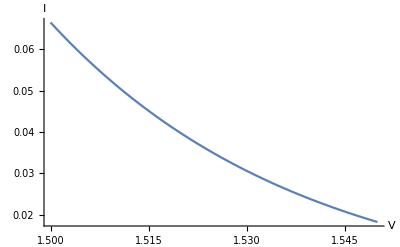

```mathematica
Plot[Vittoz[v],{v,1.5,1.55},AxesLabel->{"V","I"}]
```

```mathematica
vrange = Range[vdiode,vmax,vstep];
{Min[Vittoz[vrange]],Max[Vittoz[vrange]]}
```

{0.0000361165,3131.22}

### DAC Theory

If you have a systematic bias of 49% of the current (as opposed to a perfect binary 50%) split, then what is the final value after 10 bits.  Of course, this is trying to approximate the worst case if you have a 1% mismatch between two transistor sizes.  The reason this is worst case is b/c in some cases, you could have 1% bias the other way (51%) which would cancel the eventual deviation.

```mathematica
(49/100)^10//N
```

0.000797923

Compare the number above to the perfect transistor pair, which means a perfect 50% split in the current.

```mathematica
(1/2)^10//N
```

0.000976563

```mathematica
PadLeft[IntegerDigits[100,2],10]
```

{0,0,0,1,1,0,0,1,0,0}

Evaluate the deviation on a bit by bit basis.  10 bits out should match the numbers above.

```mathematica
binaryDeviation=Table[(0.49)^i,{i,1,10}] 
binaryDeviation1=Table[(0.5)^i,{i,1,10}]
```

{0.49,0.2401,0.117649,0.057648,0.0282475,0.0138413,0.00678223,0.00332329,0.00162841,0.000797923}

{0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195313,0.000976563}

Evaluate the analog value if you set the DAC bits to the x-value

```mathematica
Plus@@(PadLeft[IntegerDigits[100,2],10] binaryDeviation)
```

0.0892188

Plot the function with DAC value on the x-axis, and the analog value on the y-axis.  The difference between foo1 and foo is the maximum error if you assume a maximum percentage error due to mismatch, as calculated into binaryDeviation

```mathematica
foo =Table[Plus@@(PadLeft[IntegerDigits[n,2],10] binaryDeviation),{n,1,1023}];
foo1 =Table[Plus@@(PadLeft[IntegerDigits[n,2],10] binaryDeviation1),{n,1,1023}];
```

```mathematica
PlotStyle->PointSize[Small],
```

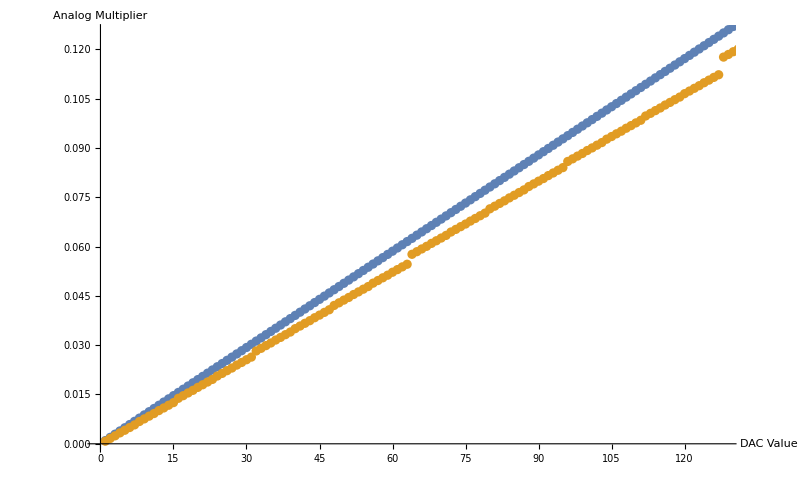

```mathematica
p=ListPlot[{foo1,foo},ImageSize-> 250];
ListPlot[{foo1,foo},PlotRange->{{0,128},{0,1/8}},ImageSize-> 800,Epilog->Inset[p,{10,1/8},{Left,Top}],AxesLabel->{"DAC Value","Analog Multiplier"}]
```